{ϕ[0],ϕ[1]}

{{ϕ[0]→-4.99884×10^-16+2.59026 ⅈ,ϕ[1]→-2.61283×10^16-2.8939×10^-16 ⅈ}}

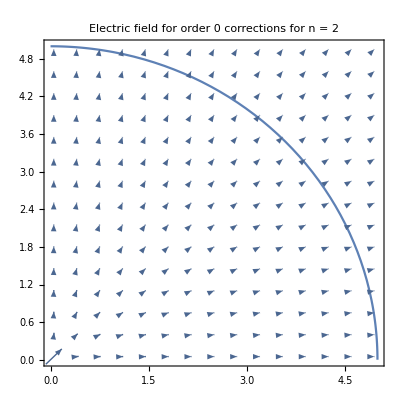

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=0;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 7.01165×10^-6-0.00385667 ⅈ and 0.0319759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 7.01165×10^-6-0.00385667 ⅈ and 0.0319759 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -0.00109843+0.0000913122 ⅈ and 0.0569005 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.251327+0. ⅈ,3.48787×10^-16+4.35984×10^-17 ⅈ,6.28319+0. ⅈ,3.31348×10^-17+1.56954×10^-17 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«4»,{1.40233×10^-6-0.000771334 ⅈ,0.013685-0.0135858 ⅈ,0.0000350582-0.0192833 ⅈ,0.000547399-0.000543432 ⅈ,2.51902×10^-16+2.19325 ⅈ,0.+0. ⅈ,6.58177+5.73058×10^16 ⅈ}} may contain significant numerical errors.

{ϕ[0],ϕ[1],A[-1],A[1],B[-1],B[1]}

{{ϕ[0]→1.68268×10^-16-3.08781×10^-16 ⅈ,ϕ[1]→-3.262×10^-17-9.83747×10^-17 ⅈ,A[-1]→0.423451-0.390045 ⅈ,A[1]→0.0112719-0.0306606 ⅈ,B[-1]→-0.016938+0.0156018 ⅈ,B[1]→-0.281798+0.766516 ⅈ}}

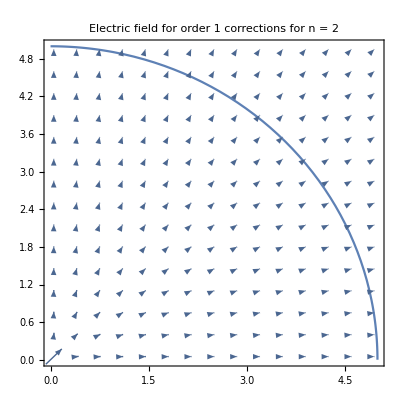

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=1;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273699-0.00271716 ⅈ and 0.0311647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273699-0.00271716 ⅈ and 0.0311647 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 5.2593×10^-6-0.00192833 ⅈ and 0.0474239 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.0643261-3.83666×10^-18 ⅈ,0.251327+0. ⅈ,3.48787×10^-16+4.35984×10^-17 ⅈ,13.9626+2.6159×10^-15 ⅈ,40.2038-1.24255×10^-14 ⅈ,6.28319+0. ⅈ,3.31348×10^-17+1.56954×10^-17 ⅈ,0.0223402+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},«8»,{1.65674×10^-17-2.6159×10^-17 ⅈ,«9»,1.28934-3.74037×10^16 ⅈ}} may contain significant numerical errors.

{ϕ[0],ϕ[1],A[-2],A[-1],A[1],A[2],B[-2],B[-1],B[1],B[2]}

{{ϕ[0]→-1.7142×10^-13+7.85575×10^-15 ⅈ,ϕ[1]→-4.37839×10^-17+7.9253×10^-17 ⅈ,A[-2]→0.983557-0.0333207 ⅈ,A[-1]→0.03909+0.0697621 ⅈ,A[1]→0.000220258+0.006078 ⅈ,A[2]→0.0000704912+1.25775×10^-7 ⅈ,B[-2]→-0.00157369+0.0000533131 ⅈ,B[-1]→-0.0015636-0.00279048 ⅈ,B[1]→-0.00550644-0.15195 ⅈ,B[2]→-0.044057-0.0000786097 ⅈ}}

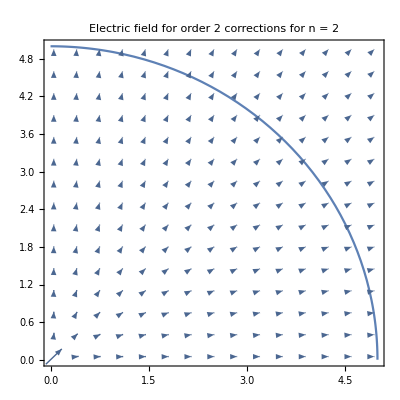

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=2;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained -2.66812×10^-7+0.000260902 ⅈ and 0.0168585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.71171}. NIntegrate obtained -2.66812×10^-7+0.000260902 ⅈ and 0.0168585 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00273699-0.00271716 ⅈ and 0.0311647 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {«1»} may contain significant numerical errors.

{ϕ[0],ϕ[1],A[-3],A[-2],A[-1],A[1],A[2],A[3],B[-3],B[-2],B[-1],B[1],B[2],B[3]}

{{ϕ[0]→2.08383×10^-13+1.63381×10^-14 ⅈ,ϕ[1]→1.29835×10^-16+1.46725×10^-16 ⅈ,A[-3]→0.979855+0.0282804 ⅈ,A[-2]→-0.0595926-0.00102547 ⅈ,A[-1]→-0.185142+0.00494208 ⅈ,A[1]→-0.00097361-0.000845687 ⅈ,A[2]→-0.0000184242-2.41912×10^-7 ⅈ,A[3]→4.90739×10^-8-2.2947×10^-8 ⅈ,B[-3]→-0.0000627107-1.80994×10^-6 ⅈ,B[-2]→0.0000953481+1.64076×10^-6 ⅈ,B[-1]→0.00740567-0.000197683 ⅈ,B[1]→0.0243403+0.0211422 ⅈ,B[2]→0.0115151+0.000151195 ⅈ,B[3]→-0.00076678+0.000358547 ⅈ}}

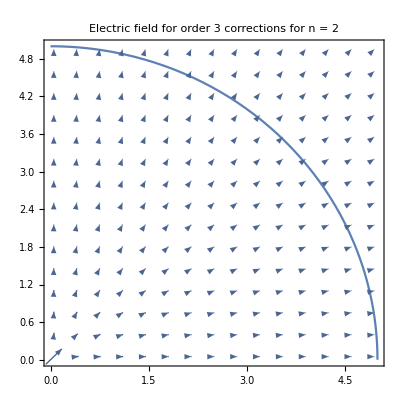

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=3;(* Half the number of coefficients Am or Bm *)
n=2;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {5.50938}. NIntegrate obtained 1.65246×10^-6-0.000629141 ⅈ and 0.00559498 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15318}. NIntegrate obtained -0.00617366+0.571721 ⅈ and 0.0102141 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15318}. NIntegrate obtained -6.28531-0.0275369 ⅈ and 0.0622656 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{ϕ[0],ϕ[1],A[-1],A[1],B[-1],B[1]}

{{ϕ[0]→630.361+373.371 ⅈ,ϕ[1]→-2.61283×10^16+0.550656 ⅈ,A[-1]→88899.7-22811.4 ⅈ,A[1]→-4293.57+995.6 ⅈ,B[-1]→-3757.9+777.206 ⅈ,B[1]→107557.-28168.9 ⅈ}}

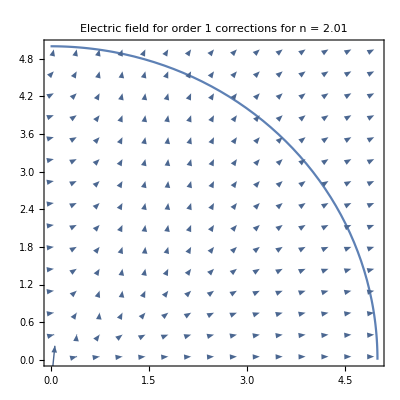

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=1;(* Half the number of coefficients Am or Bm *)
n=2.01;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.00275557-0.00270831 ⅈ and 0.03131 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58239}. NIntegrate obtained 0.00273077-0.00272009 ⅈ and 0.0311216 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {4.72398}. NIntegrate obtained 0.0000116701-0.00191567 ⅈ and 0.0474021 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{ϕ[0],ϕ[1],A[-2],A[-1],A[1],A[2],B[-2],B[-1],B[1],B[2]}

{{ϕ[0]→5632.38+361.125 ⅈ,ϕ[1]→-2.61283×10^16+1.49787 ⅈ,A[-2]→8.44779×10^6-1.54289×10^6 ⅈ,A[-1]→89332.-1.88815×10^6 ⅈ,A[1]→-24187.8+73642.6 ⅈ,A[2]→17507.2+1067.83 ⅈ,B[-2]→-6977.08+10648.4 ⅈ,B[-1]→66278.+122899. ⅈ,B[1]→2.1429×10^6-2.8864×10^6 ⅈ,B[2]→-8.45132×10^6-90804.2 ⅈ}}

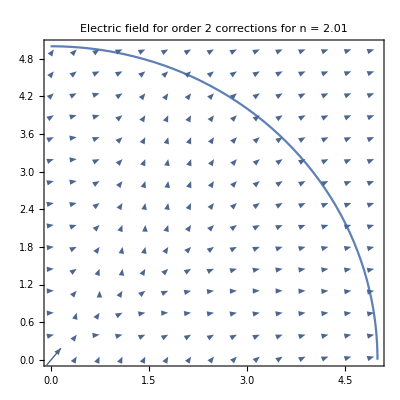

```mathematica
Block[
{M,kMax,m,k,n,R,Ia,Ib,Ic,Id,Ie,eq1,eq2,A,B,ϕ,q,ϵ0,soln,Er,Et,matrix,var},
M=2;(* Half the number of coefficients Am or Bm *)
n=2.01;(* Exponents of x^n+y^n=R^n*)
R=5;(* The span size of the conveyor belt *)
q=1452897;(* Linear charge density = 1452897 C/m <--> A linear density of charges in a AWG guage 0000 *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
Ia=<||>;Ib=<||>;Ic=<||>;Id=<||>;Ie=<||>;
For[
m=-M,m≤M,m++,
For[
k=1,k≤2M,k++,
Ia=Append[Ia,{m,k}-> NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^(m-1)(1+Tan[θ]^n)^((m-1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ib=Append[Ib,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^(m+1)(1+Tan[θ]^n)^((m+1)/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
];
For[
k=0,k≤2M+1,k++,
Ic=Append[Ic,k-> NIntegrate[Log[Cos[θ](1+Tan[θ]^n)^(1/n)]Exp[-I k θ],{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Id=Append[Id,{m,k}->NIntegrate[Exp[I(m-k) θ]/(Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
Ie=Append[Ie,{m,k}-> NIntegrate[Exp[I(m-k) θ](Cos[θ]^m(1+Tan[θ]^n)^(m/n)),{θ,0,2π},AccuracyGoal->11,Method->"RiemannRule"]];
]
];
eq1=Table[Total[Table[m A[m]R^(m-1)Ia[{m,k}]+m B[m]/R^(m+1) Ib[{m,k}],{m,-M,M}]]==0,{k,1,2M}];
eq2=Table[2π ϕ[0] DiscreteDelta[k]+(ϕ[1]+q/(2π ϵ0))Ic[k]+Total[Drop[Table[A[m]R^m Id[{m,k}]+B[m]/R^m Ie[{m,k}],{m,-M,M}],{M+1}]]==0,{k,0,2M+1}];
var=Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]];
soln=Solve[Join[eq1,eq2],var,WorkingPrecision->100];
matrix=Normal@CoefficientArrays[Join[eq1,eq2],Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]][[2]];
soln=If[Length[soln]==0,{Table[var[[m]]->NullSpace[matrix][[1]][[m]],{m,1,Length[var]}]},soln];
Print[Join[{ϕ[0],ϕ[1]},Drop[Table[A[m],{m,-M,M}],{M+1}],Drop[Table[B[m],{m,-M,M}],{M+1}]]];
Print[soln];
Er[x_,y_]:=Part[((ϕ[1]+q/(2π ϵ0))/(√(x^2+y^2))+Total[Drop[Table[-ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (-B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Et[x_,y_]:=Part[(Total[Drop[Table[-ⅈ ⅇ^(ⅈ m ArcTan[x,y]) m (x^2+y^2)^(-1/2-m/2) (B[m]+A[m] (x^2+y^2)^m),{m,-M,M}],{M+1}]])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2}],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```